# SHARAQ04 knockout Simulation

```mathematica
c=299.792458;
mp=938.27205;
mn=939.56538;
md=1875.612858;
mHe4=3727.379;
mB11=10252.548;
mC12=11174.863;
mN13=12111.191;
mN21=19586.63;
mO13=12128.447;
mO14=13044.836;
mO21=19565.350;
mO22=20498.066;
mO23=21434.888;
mO24=22370.840;
mF23=21423.077;
mF24=22358.818;
mF25=23294.116;
m28Si=26053.187104;
m30P=27916.95645;
massList={mp->"π",mn->"μ",md->"D",mHe4->"α",mB11->"B11",mC12->"C12",mN13->"N13",mN21->"N21",mO13->"O13",mO14->"O14",mO21->"O21",mO22->"O22",mF23-> "F23", mF25->"F25",m28Si->"28Si",m30P->"30P"};
vO={0,0,0};
vX={1,0,0};
vY={0,1,0};
vZ={0,0,1};
```

## Auxiliary functions (must declare)

```mathematica
mE2k[m_,E_]:=√(E^2-m^2);mE2T[m_,E_]:=E-m;
mk2E[m_,k_]:=√(m^2+k^2);mk2T[m_,k_]:=√(m^2+k^2)-m;
mT2E[m_,T_]:=m+T;mT2k[m_,T_]:=√((m+T)^2-m^2);
Ek2m[E_,k_]:=√(E^2-k^2);Ek2T[E_,k_]:=E-√(E^2-k^2);
ET2m[E_,T_]:=E-T;ET2k[E_,T_]:=√(E^2-(E-T)^2);
kT2m[k_,T_]:=(k^2-T^2)/(2 T);kT2E[k_,T_]:=(k^2+T^2)/(2 T);
Momt[V_]:=√(V[[2]]^2+V[[3]]^2+V[[4]]^2);
Mass[V_]:=√(V[[1]]^2-Momt[V]^2)
KE[V_]:=V[[1]]-Mass[V];
Angle[V_]:=If[V[[2]]==0 && V[[3]]==0,{0,0},{ArcTan[V[[4]],√(V[[2]]^2+V[[3]]^2)],If[ArcTan[V[[2]],V[[3]]]<-π/2,ArcTan[V[[2]],V[[3]]]+2π,ArcTan[V[[2]],V[[3]]]]}];
AngleRev[V_]:=If[V[[2]]==0 && V[[3]]==0,{0,0},{ArcTan[-V[[4]],√(V[[2]]^2+V[[3]]^2)],If[ArcTan[V[[2]],V[[3]]]<-π/2,ArcTan[V[[2]],V[[3]]]+2π,ArcTan[V[[2]],V[[3]]]]}];
β[V_]:=Momt[V]/V[[1]];
DisVector[V_,name_]:={name,V[[1]],V[[2]],V[[3]],V[[4]]};
DisEnergy[V_,m_,name_]:={name,V[[1]]-m,Momt[V],Angle[V][[1]] 180/π,Angle[V][[2]] 180/π};
vect[V_]:=Drop[V,{1}];
line[Vstart_,Vend_]:={If[Length[Vstart]==4,vect[Vstart],Vstart],If[Length[Vstart]==4,vect[Vstart],Vstart]+If[Length[Vend]==4,vect[Vend],Vend]};
crossN[V_,U_]:=Join[{0},Cross[vect[V],vect[U]]/(Momt[V] Momt[U])];
Δθ[V_,U_]:=ArcCos[(vect[V].vect[U])/(Momt[V]Momt[U])];
β2γ[β_]:=1/(√(1-β^2));
γ2β[γ_]:=√(1-1/γ^2);
KEA2β[KEA_,A_,m_]:=mT2k[m,KEA A]/mT2E[m,KEA A];
Bρ2KEA[Bρ_,Z_,A_, m_]:=(√((Bρ Z c)^2+m^2)-m)/A;
KEA2Bρ[KEA_,Z_,A_,m_]:=m/(Z c) KEA2β[KEA,A,m] β2γ[KEA2β[KEA,A,m] ]
```

## Kncockout Kinematics

```mathematica
PmE[m_,E_,θ_,ϕ_]:={E,mE2k[m,E] Sin[θ]Cos[ϕ],mE2k[m,E] Sin[θ]Sin[ϕ],mE2k[m,E] Cos[θ]};
Pmk[m_,k_,θ_,ϕ_]:={mk2E[m,k],k Sin[θ] Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]};
PmT[m_,T_,θ_,ϕ_]:={m+T,mT2k[m,T]Sin[θ] Cos[ϕ],mT2k[m,T]Sin[θ]Sin[ϕ],mT2k[m,T] Cos[θ]};
PEk[E_,k_,θ_,ϕ_]:={E,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]};
PET[E_,T_,θ_,ϕ_]:={E,ET2k[E,T] Sin[θ]Cos[ϕ],ET2k[E,T]  Sin[θ]Sin[ϕ],ET2k[E,T]  Cos[θ]};
PkT[k_,T_,θ_,ϕ_]:={kT2E[k,T],k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]};
```

```mathematica
(* basis right-hand rotation operator *)
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}};
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}};
R[α_,θ_,ϕ_]:=Rz[-ϕ].Ry[-θ].Rz[α].Ry[θ].Rz[ϕ];
(* coordinate transform *)
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[-ϕ].Ry[-θ].Lz[β].Ry[θ].Rz[ϕ]
```

```mathematica
L[b,θ,ϕ]//Simplify//MatrixForm
L[b,θ,0]//MatrixForm
```

(1/(√(1-b^2)) | (b Cos[ϕ] Sin[θ])/(√(1-b^2)) | (b Sin[θ] Sin[ϕ])/(√(1-b^2)) | (b Cos[θ])/(√(1-b^2))
(b Cos[ϕ] Sin[θ])/(√(1-b^2)) | Cos[ϕ]^2 (Cos[θ]^2+Sin[θ]^2/(√(1-b^2)))+Sin[ϕ]^2 | Cos[ϕ] (-1+Cos[θ]^2+Sin[θ]^2/(√(1-b^2))) Sin[ϕ] | (-1+1/(√(1-b^2))) Cos[θ] Cos[ϕ] Sin[θ]
(b Sin[θ] Sin[ϕ])/(√(1-b^2)) | Cos[ϕ] (-1+Cos[θ]^2+Sin[θ]^2/(√(1-b^2))) Sin[ϕ] | Cos[ϕ]^2+(Cos[θ]^2+Sin[θ]^2/(√(1-b^2))) Sin[ϕ]^2 | (-1+1/(√(1-b^2))) Cos[θ] Sin[θ] Sin[ϕ]
(b Cos[θ])/(√(1-b^2)) | (-1+1/(√(1-b^2))) Cos[θ] Cos[ϕ] Sin[θ] | (-1+1/(√(1-b^2))) Cos[θ] Sin[θ] Sin[ϕ] | Cos[θ]^2/(√(1-b^2))+Sin[θ]^2)

(1/(√(1-b^2)) | (b Sin[θ])/(√(1-b^2)) | 0 | (b Cos[θ])/(√(1-b^2))
(b Sin[θ])/(√(1-b^2)) | Cos[θ]^2+Sin[θ]^2/(√(1-b^2)) | 0 | -Cos[θ] Sin[θ]+(Cos[θ] Sin[θ])/(√(1-b^2))
0 | 0 | 1 | 0
(b Cos[θ])/(√(1-b^2)) | -Cos[θ] Sin[θ]+(Cos[θ] Sin[θ])/(√(1-b^2)) | 0 | Cos[θ]^2/(√(1-b^2))+Sin[θ]^2)

```mathematica
{0,0,0,1}.Ry[θNN].Rz[ϕNN].Ry[θ].Rz[ϕ]//FullSimplify//MatrixForm
```

(0
Cos[θNN] Cos[ϕ] Sin[θ]+Sin[θNN] (Cos[θ] Cos[ϕ] Cos[ϕNN]-Sin[ϕ] Sin[ϕNN])
Cos[θNN] Sin[θ] Sin[ϕ]+Sin[θNN] (Cos[θ] Cos[ϕNN] Sin[ϕ]+Cos[ϕ] Sin[ϕNN])
Cos[θ] Cos[θNN]-Cos[ϕNN] Sin[θ] Sin[θNN])

```mathematica
Manipulate[Graphics3D[{
{Gray,Line[{{0,0,0},{1,0,0}}]},Text["x",{1,0,0}],
{Gray,Line[{{0,0,0},{0,1,0}}]},Text["y",{0,1,0}],
{Gray,Line[{{0,0,0},{0,0,1}}]},Text["z",{0,0,1}],
{Red,Arrow[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]},
{Green, Arrow[{{0,0,0},Evaluate[Drop[ {0,0,0,1}.Ry[θNN].Rz[ϕNN].Ry[θ].Rz[ϕ],{1}]]}]},
{Blue,Arrow[{{0,0,0},Evaluate[Drop[{0,Sin[θNN]Cos[ϕNN],Sin[θNN]Sin[ϕNN],Cos[θNN]}.R[α,θ,ϕ],{1}]]}]}
},PlotRange->1,ViewPoint->{15,10,7}],{θ,0,π},{ϕ,0,2π},{θNN,0,π},{ϕNN,0,2π},{α,0,2π}]
```

### Simulation

```mathematica
(* reaction  Normal kinematics A(a,a'+b)B , A = B+b  *)
```

```mathematica
knockout[k_,θk_,ϕk_,θNN_,ϕNN_,S_,mA_,ma_,mb_,TaL_]:={
Pa = PmT[ma,TaL,0,0]; (* incident proton *)
PA=PmT[mA,0,0,0]; (* Target *)
PB=Pmk[mA-mb+S,k,θk,ϕk]; (* residual *)
Pn=PA-PB; (* psudo orbital nucleon *)
PN=If[θk==0,{0,0,1,0},crossN[Pa,Pn]]; (* perpendicular vector of Pa and Pn , default y-axis*)
{θrot,ϕrot}=Angle[PN];
Pc = (Pa+Pn)/2;
βPc = β[Pc];
{θPc,ϕPc}=Angle[Pc];
(* in CM frame *)
Pcc=Pc.L[-βPc,θPc,ϕPc];
Pac=Pa.L[-βPc,θPc,ϕPc];
Pnc=Pn.L[-βPc,θPc,ϕPc];
{θac,ϕac}=Angle[Pac];
Etotal=√(1-βPc^2)(Pa[[1]]+Pn[[1]]); (* total energy of E1c and E2c in CM frame*)
k1c=1/(2 Etotal)(√((Etotal-ma-mb)(Etotal+ma-mb) (Etotal-ma+mb) (Etotal+ma+mb)));
P1c = {√(ma^2+k1c^2), 0,0,k1c}.(*Ry[θNN].Rz[ϕNN].*)Ry[θac+θNN].Rz[ϕac+ϕNN];
P2c ={√(ma^2+k1c^2), 0,0,k1c}.(*Ry[π+θNN].Rz[ϕNN].*)Ry[θac+θNN+π].Rz[ϕac+ϕNN];
(*P1c={√(ma^2+k1c^2),k1c Sin[θac]Cos[ϕac],k1c Sin[θac]Sin[ϕac], k1c Cos[θac]}.R[θNN,θrot,ϕrot].R[ϕNN,θac,ϕac];*)
(*P2c={√(mb^2+k1c^2) ,k1c Sin[θac]Cos[ϕac],k1c Sin[θac]Sin[ϕac], k1c Cos[θac]}.R[θNN+π,θrot,ϕrot].R[ϕNN,θac,ϕac];*)
P1=P1c.L[βPc,θPc,ϕPc];
P2=P2c.L[βPc,θPc,ϕPc];
βPa=β[Pa];γPa=γ2β[β[Pa]] ;
PaL=Pa.L[-βPa,0,0];
PAL=PA.L[-βPa,0,0];
PBL=PB.L[-βPa,0,0];
PnL=Pn.L[-βPa,0,0];
P1L=P1.L[-βPa,0,0];
P2L=P2.L[-βPa,0,0];
SepOnline=ma-γPa mb-(γPa  (P1L[[1]]-ma+P2L[[1]]-mb)- βPa γPa (Abs[P1L[[4]]+P2L[[4]]]));
Sep=Mass[PAL+PaL-P1L-P2L]-(mA-mb);
(* output *)
PaL, PAL,P1L,P2L,P1,P2
}
```

```mathematica
size=500;
Manipulate[knockout[k,θk,ϕk,θNN,ϕNN,S,mO14,mp,mp,250];
Graphics3D[{
Black,Text["x",size (1.1)vX], Arrow[line[vO,size vX]],Arrow[line[vO,size vY]],Arrow[line[vO,size vZ]],
Orange,Arrow[Reverse[line[vO,-Pa]]],
Pink,Arrow[line[vO,PB]],
Purple,Arrow[line[vO,Pn]],
Green,Arrow[line[vO,Pc]],
Red,Arrow[line[vO,P1]],
Blue,Arrow[line[vO,P2]],
Blue,Arrow[line[P1,P2]],
Pink,Arrow[line[P1+P2,PB]],
Gray,Arrow[line[vO,P1+P2+PB]],
Black, Text[Sep,-Pa[[2;;4]]]
}]
,{{k,200},0,300},{{θk,π/2},0,2π},{ϕk,0,2π},{{θNN,π/2},0,2π},{{ϕNN,π/6},0,2π},{{S,1},0,2π}]
```

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mO,m1,m2,TiL];
TableForm[
{{NumberForm[TableForm[Chop[{
"Setting",
{"TKA",TiL},
{"k",k,"θk, ϕk",θk ,ϕk  },{"S",S,"θNN, ϕNN",θNN ,ϕNN },
{"βPa",βPa},
{"SepOnline", SepOnline},
{"Sep", Sep},
{"Lab frame", "----", "----", "----"},DisVector[PaL,"PaL"],DisVector[PAL,"PAL"],DisVector[PnL,"PnL"],DisVector[P1L,"P1L"],DisVector[P2L,"P2L"],"",
{"", "K.E." , "Momentum", "θ" , "ϕ"},DisEnergy[P1L,m1,"P1L"] ,DisEnergy[P2L,m2,"P2L"],{"T1L+T2L", KE[P1L]+KE[P2L]},{"β1" , β[P1L]},{"β2" , β[P2L]},(2π-Angle[P1L]-Angle[P2L])180/π,
{"O frame ", "----", "----", "----"},DisVector[Pa,"Pa"],DisVector[Pn,"Pn"],DisEnergy[Pn,m2,""],DisVector[P1,"P1"],DisVector[P2,"P2"],DisVector[P1+P2-Pa-Pn,"Diff"],
{"", "K.E." , "Momentum", "θ" , "ϕ"},DisEnergy[P1,m1,"P1"] ,DisEnergy[P2,m2,"P2"],{"T1+T2", KE[P1]+KE[P2], "T1+T2+S", KE[P1]+KE[P2]+S},{"β1" , β[P1], "TB", KE[PB]},
{"Lorentz", "----", "----", "----"},DisVector[Pc,"Pc"],DisEnergy[Pc,0,""],{"β" , βPc,"γ", 1/(√(1-βPc^2))},DisVector[Pcc,"pcc"],
{"CM frame", "----", "----", "----"},DisVector[Pac,"Pac"],DisEnergy[Pac,m1,""],DisVector[Pnc,"Pnc"],DisVector[P1c,"k1c"],DisVector[P2c,"P2c"],{"Δθ[Pac,P1c]",Δθ[Pac,P1c] 180/π},
{KE[PAL]/25}
}],TableAlignments->{Right}],6],
Graphics[{
{Black,Arrow[{{-PAL[[2]],-PAL[[4]]},{0,0}}]},
{Pink, Arrow[{{0,0},{PBL[[2]],PBL[[4]]}}]},
{Blue,Arrow[{{0,0},{P1L[[2]],P1L[[4]]}}]},
{Red,Arrow[{{0,0},{P2L[[2]],P2L[[4]]}}]},
{Orange,Arrow[{{-PnL[[2]],-PnL[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Lab, S="<>ToString[S]<>", k="<>ToString[k]<>", θ_k="<>ToString[θk ]<>"°, θ_NN="<>ToString[θNN ]<>"°, ΣT="<>ToString[DisEnergy[P2L,m2,""][[2]]+DisEnergy[P1L,m1,""][[2]]],Epilog->{Text["θ1L="<>ToString[180-Angle[P1L][[1]] 180/π]<>"\nβ1="<>ToString[β[P1L]]<>"\nT1="<>ToString[DisEnergy[P1L,m1,""][[2]]],{P1L[[2]],P1L[[4]]-90}],Text["θ2L="<>ToString[180-Angle[P2L][[1]] 180/π]<>"\nβ2="<>ToString[β[P2L]]<>"\nT2="<>ToString[DisEnergy[P2L,m2,""][[2]]],{P2L[[2]],P2L[[4]]-90}],
Text["Nucleus",{Pa[[2]]+150,Pa[[4]]-100}],
Text["Orbital Neutron",{-PnL[[2]]-200,-PnL[[4]]-50}],
Text["ΔAngle="<>ToString[Δθ[P1L,P2L] 180/π],{0,-620}]},ImageSize->400],
{Graphics[{
{Purple,Arrow[{{-Pa[[2]],-Pa[[4]]},{0,0}}]},
{Pink, Arrow[{{0,0},{PB[[2]],PB[[4]]}}]},
{Blue,Arrow[{{0,0},{P1[[2]],P1[[4]]}}]},
{Red,Arrow[{{0,0},{P2[[2]],P2[[4]]}}]},
{Green,Arrow[{{0,0},{Pc[[2]],Pc[[4]]}}]},
{Orange,Arrow[{{-Pn[[2]],-Pn[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Nucleus",ImageSize->250]
,
Graphics[{{Purple,Arrow[{{-Pac[[2]],-Pac[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1c[[2]],P1c[[4]]}}]},
{Red,Arrow[{{0,0},{P2c[[2]],P2c[[4]]}}]},
{Orange,Arrow[{{-Pnc[[2]],-Pnc[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "C.Momemtum",
Epilog->{Text["T_tot="<>ToString[DisEnergy[Pac,mp,""][[2]]+DisEnergy[Pnc,mn,""][[2]]]<>"\n θa, ϕc ="<>ToString[θac / Degree]<>", "<>ToString[ϕac/Degree],{0,500}]},ImageSize->250]
}
}
}],
{{m1,mp},{mp->"Proton",mn->"Neutron"}},
{{m2,mp},{mp->"Proton",mn->"Neutron",mHe4->"alpha",md->"D"}},
{{mO,mF23},massList},
{{TiL,289.55},0,300},
{{k,100},{0,10,20,50,100,150,170,200,220,270}},
{{θk,60},-180,180},
{{ϕk,00},-180,180},
{{S,13.26},0,30},
{{θNN,60},-180,180},
{{ϕNN,0},-180,360},ControlPlacement->Top]
```

```mathematica
Findpd[Tc_,θc_,ϕc_,θd_,ϕd_,S_,mA_,ma_,mb_,TaL_]:=Module[{a,b,d,Δ,pa,pc,mr,AA,BB,CC},
a=TaL-Tc+mA;
Δ=Cos[θc]Cos[θd]+Sin[θc]Sin[θd]Cos[ϕc-ϕd];
mr=S+mA-mp;
pa=√(2mp TaL+TaL^2);
pc=√(2mp Tc+Tc^2);
b=mr^2+pc^2+pa^2-2pa pc Cos[θc];
d=-2pa Cos[θd]+2pc Δ;
AA=4 a^2-d^2;
BB=2(a^2+mp^2-b) d;
CC=4 a^2 mp^2-(a^2+mp^2-b)^2;
{(-BB-√(BB^2-4AA CC))/(2AA),(-BB+√(BB^2-4AA CC))/(2AA)}
]
```

```mathematica
JJ=knockout[100,80 °,0 °,60 °,0 °,0,mO14,mp,mp,200];
KE[JJ[[4]]]
Experiment[KE[JJ[[3]]],Angle[JJ[[3]]][[1]],Angle[JJ[[3]]][[2]],KE[JJ[[4]]],Angle[JJ[[4]]][[1]],Angle[JJ[[4]]][[2]], mO14,mp,mN13,mp, 200]//TableForm
DisEnergy[JJ[[5]],mp,"P1"]
DisEnergy[JJ[[6]],mp,"P2"]
Findpd[KE[JJ[[5]]],Angle[JJ[[5]]][[1]],Angle[JJ[[5]]][[2]],Angle[JJ[[6]]][[1]],Angle[JJ[[6]]][[2]],0,mO14,mp,mp,200]
```

158.552

100. | 
100. | 180.
0. | 
60. | 1.3441×10^-30

{P1,120.1,489.692,29.4686,-7.01671×10^-15}

{P2,79.4865,394.307,59.3961,180.}

{-345.364,394.307}

### Experiment

```mathematica
Experiment[T1L_,θ1L_,ϕ1L_,T2L_,θ2L_,ϕ2L_,mA_,ma_,mR_,mb_,TaL_]:=
{
P1XL=PmT[ma,T1L,θ1L,ϕ1L];
P2XL=PmT[mb,T2L,θ2L,ϕ2L];
βaX=mT2k[ma,TaL]/mT2E[ma,TaL];
(* change to Nucleus frame *)
PAX=PmT[mA,0,0,0];
PAXL=PAX.L[-βaX,0,0];
PaX=PmT[mp,TaL,0,0];
PaXL=PaX.L[-βaX,0,0];
P1X=P1XL.L[βaX,0,0];
P2X=P2XL.L[βaX,0,0];
PnX=-PaX+P1X+P2X;
PnXL=PnX.L[βaX,0,0];
PcX=(P1X+P2X)/2;
βPcX=β[PcX];
{θPcX,ϕPcX}=Angle[PcX];
(* in CM frame of a X *)
PcXc=PcX.L[-βPcX,θPcX,ϕPcX];
PaXc=PaX.L[-βPcX,θPcX,ϕPcX];
PnXc=PnX.L[-βPcX,θPcX,ϕPcX];
P1Xc=P1X.L[-βPcX,θPcX,ϕPcX];
P2Xc=P2X.L[-βPcX,θPcX,ϕPcX];
θNNX=Δθ[PaXc,P1Xc] 180/π;
SepXL=Mass[PAXL+PaXL-P1XL-P2XL]-(mA-mb);
γaX=1/(√(1-βaX^2));
(*out put*)
Momt[PnX],
Angle[PnX] 180/π,
SepX=Mass[PaX+PAX-P1X-P2X]-(mA-mb),
(*Ex=mA-mb-mR+SepX,*)
(*SepXonline=(ma-γaX mb)-γaX(T1L+T2L)+γaX βaX(Abs[P1XL[[4]]+P2XL[[4]]]),*)
{θaXc,ϕaXc}=Angle[PaXc];
Angle[P1Xc.Rz[-ϕaXc].Ry[-θaXc]]180/π (* θNN, ϕNN *)
}
```

```mathematica
Experiment[119.521,129.955 °, -180 °, 119.521, 145.819 °, 0, mO14,mp,mN13,mp, 245.4]
```

{100.003,{89.9999,180.},4.62685,{90.,180.}}

## Correlation Plots

```mathematica
T1θ1List5060=Table[temp=knockout[50,60Degree,0,θNN Degree,0,13.26,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List10060=Table[temp=knockout[100,60Degree,0,θNN Degree,0,13.26,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0,360,2}];
T1θ1List20060=Table[temp=knockout[200,60Degree,0,θNN Degree,0,13.26,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List10030=Table[temp=knockout[100,30Degree,0,θNN Degree,0,13.26,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List10090=Table[temp=knockout[100,90Degree,0,θNN Degree,0,13.26,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List100120=Table[temp=knockout[100,120Degree,0,θNN Degree,0,13.26,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List1006000=Table[temp=knockout[100,60Degree,0,θNN Degree,0,0,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List1006010=Table[temp=knockout[100,60Degree,0,θNN Degree,0,10,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List1006020=Table[temp=knockout[100,60Degree,0,θNN Degree,0,20,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
T1θ1List1006030=Table[temp=knockout[100,60Degree,0,θNN Degree,0,30,mF23,mp,mp,289.44][[3]];{180-Angle[temp][[1]]/Degree,KE[temp]},{θNN,0, 360,2}];
```

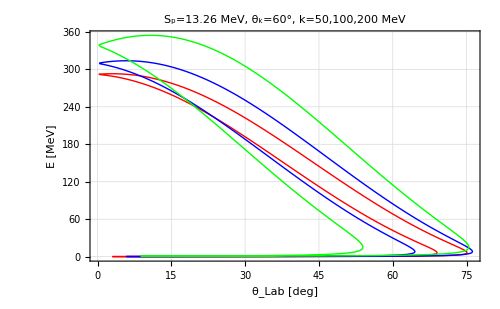

```mathematica
ListPlot[{T1θ1List5060,T1θ1List10060,T1θ1List20060},Joined->True,Frame->True,FrameLabel->{Style["θ_Lab [deg]",20],Style["E [MeV]",20]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,PlotLabel->Style["S_p=13.26 MeV, θ_k=60°, k=50,100,200 MeV",20],PlotStyle->{Red,Green,Blue}]
```

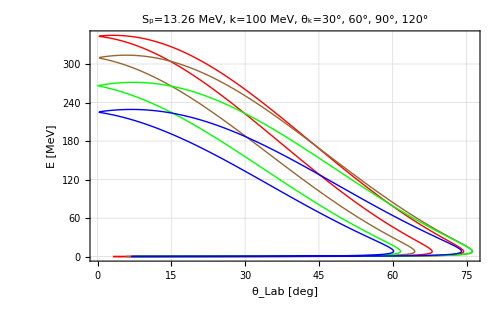

```mathematica
ListPlot[{T1θ1List10030,T1θ1List10060,T1θ1List10090,T1θ1List100120},Joined->True,Frame->True,FrameLabel->{Style["θ_Lab [deg]",20],Style["E [MeV]",20]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,PlotLabel->Style["S_p=13.26 MeV, k=100 MeV, θ_k=30°, 60°, 90°, 120°",20],PlotStyle->{Red,Brown,Green, Blue, Purple}]
```

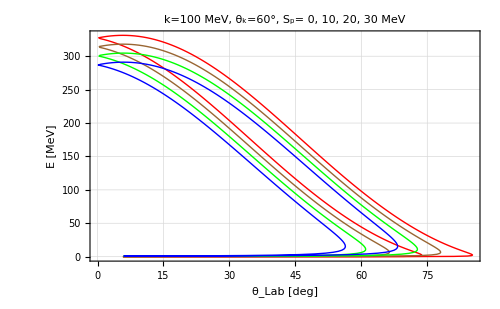

```mathematica
ListPlot[{T1θ1List1006000,T1θ1List1006010,T1θ1List1006020,T1θ1List1006030},Joined->True,Frame->True,FrameLabel->{Style["θ_Lab [deg]",20],Style["E [MeV]",20]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,PlotLabel->Style["k=100 MeV, θ_k=60°, S_p= 0, 10, 20, 30 MeV",20],PlotStyle->{Red,Brown,Green, Blue, Purple}]
```

```mathematica
EtotθList00=Table[temp=knockout[50,60Degree,0,θNN Degree,0,10,mF23,mp,mp,289.44][[3;;4]];{KE[temp[[1]]],KE[temp[[2]]]},{θNN,0, 360,2}];
EtotθList10=Table[temp=knockout[100,60Degree,0,θNN Degree,0,10,mF23,mp,mp,289.44][[3;;4]];{KE[temp[[1]]],KE[temp[[2]]]},{θNN,0, 360,2}];
EtotθList20=Table[temp=knockout[150,60Degree,0,θNN Degree,0,10,mF23,mp,mp,289.44][[3;;4]];{KE[temp[[1]]],KE[temp[[2]]]},{θNN,0, 360,2}];
```

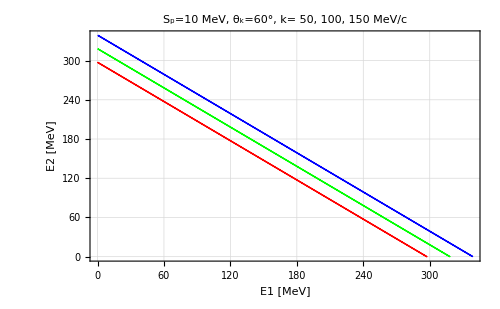

```mathematica
ListPlot[{EtotθList00, EtotθList10, EtotθList20},Joined->True,Frame->True,FrameLabel->{Style["E1 [MeV]",20],Style["E2 [MeV]",20]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,PlotLabel->Style["S_p=10 MeV, θ_k=60°, k= 50, 100, 150 MeV/c",20],PlotStyle->{Red,Green, Blue, Purple}]
```

## Detectors Resolution

### Detectors Geometry

```mathematica
z0Tpla=1400;z0=1022.37;
FL[V_]:=(2 z0Tpla)/(√3 Abs[Cos[AngleRev[V][[2]]]]Sin[AngleRev[V][[1]]]+Cos[AngleRev[V][[1]]])
ToF[V_]:=FL[V]/(β[V]c)
Sp[Ua_,UA_,V1_,V2_]:=Mass[Ua+UA-V1-V2]-Mass[UA]+Mass[V2]
SpOnline[V1_,V2_,β_]:=mp(1+1/(√(1-β^2))) -1/(√(1-β^2))(V1[[1]]+V2[[1]]-β Abs[V1[[4]]+V2[[4]]])
f[x_]:=Piecewise[{{3/2(x+170),200 2/3-170>x>-170},{200,200 (-2/3)+950>x>200 2/3-170},{-3/2(x-950),950>x>200 (-2/3)+950}},0]
MWDCPosLab[V_]:=z0/z0Tpla FL[V]{Cos[AngleRev[V][[2]]]Sin[AngleRev[V][[1]]],Sin[AngleRev[V][[2]]]Sin[AngleRev[V][[1]]],Cos[AngleRev[V][[1]]]}
MWDCPos[V_]:=RotationMatrix[π/3,{0,If[Abs[AngleRev[V][[2]]]>π/2,1,-1],0}].MWDCPosLab[V]
βbyFLTof[fl_,tof_]:=fl/(tof c);
γbyFLTof[fl_,tof_]:=(tof c)/(√(c^2 tof^2-fl^2));
γβbyFLTof[fl_,tof_]:=fl/(√(c^2 tof^2-fl^2));
New4Vector[V_,Δtof_,Δx_,Δy_]:=Module[{newMWDCPos, newFL},
newMWDCPos=MWDCPos[V]+{Δx,Δy,0};
newFL=z0Tpla/z0 Norm[newMWDCPos];
Mass[V] Join[{γbyFLTof[newFL,ToF[V]+Δtof]},γβbyFLTof[newFL,ToF[V]+Δtof]Normalize[RotationMatrix[π/3,{0,If[Abs[AngleRev[V][[2]]]>π/2,-1,1],0}].newMWDCPos]{1,1,-1}]
]
```

### Resolution

```mathematica
react=knockout[100,90 °,0 °,90 °,0 °,4.3,mO14,mp,mp,250]
```

{{938.272,0.,0.,0.},{16525.8,0.,0.,-10140.4},{1060.29,-378.225,-4.01168×10^-14,-317.493},{1060.29,278.225,-6.48844×10^-15,-407.979}}

```mathematica
Sp[react[[1]],react[[2]],react[[3]],react[[4]]]
Sp[react[[1]],react[[2]],New4Vector[react[[3]],1,0.2,1],New4Vector[react[[4]],1,1,3]]
```

4.627

4.01654

```mathematica
Manipulate[
react=knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mA,ma,mb,TiL];
{SpOrg=Sp[react[[1]],react[[2]],react[[3]],react[[4]]],
SpNew=Sp[react[[1]],react[[2]],New4Vector[react[[3]],Δtof,Δx,Δy],New4Vector[react[[4]],Δtof,Δx,Δy]],SpOrg-SpNew,ToString[(1-SpNew/SpOrg)100]<>"%"}
,{{ma,mp},{mp->"Proton",mn->"Neutron"}},{{mb,mp},{mp->"Proton",mn->"Neutron",mHe4->"alpha"}},{{mA,mO14},massList},{{TiL,245.4},0,300},{{k,100},{0,50,100,150,200,270}},{{θk,90},-180,180},{{ϕk,0},-180,180},{{S,4.627},0,30},{{θNN,90},-180,180},{{ϕNN,0},-180,360},{{Δx,0},-1,1},{{Δy,0},-3,3},{{Δtof,0},-1,1},ControlPlacement->Left]
```

## Monte Carlo Simulation

```mathematica
n=50000;
TKEA=289;
(*TKEA=Table[Bρ2KEA[7.117+RandomReal[{-0.1,0.1}],9,25,mF25]25 *mp/mF25,{i,1,n}];*)
(*TKEA=RandomVariate[TriangularDistribution[{Bρ2KEA[7.117-0.1,9,25,mF23]23 *mp/mF23,Bρ2KEA[7.117+0.1,9,25,mF25]25 *mp/mF25},Bρ2KEA[7.117+0.1,9,25,mF25]25 *mp/mF25],n];*)
kList=Table[RandomReal[{0,250}],{i,1,n}];
(*SpList=Table[RandomChoice[{4.627}(*+{0,3.5,9.54,11.74}*)],{i,1,n}];*)
SpList=Table[RandomChoice[{13.26}],{i,1,n}];
(*SpList =Table[RandomChoice[13.26+{0, 3.199,4.582, 4.909}],{i,1,n}];(* 23F *) *)
(*SpList=Table[RandomChoice[14.43+{0, 4.79,5.37, 7.6}],{i,1,n}];(* 25F *)*)
θkList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕkList=Table[ π RandomReal[{-1,1}],{i,1,n}];
θNNList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕNNList=Table[π RandomReal[{-1,1}],{i,1,n}];
reactList=Table[knockout[kList[[i]],θkList[[i]],ϕkList[[i]],θNNList[[i]],ϕNNList[[i]],SpList[[i]],mF23,mp,mp,TKEA],{i,1,n}];
```

```mathematica
(* Rearrange List by Left and Right *)
ArrgList = Table[If[reactList[[k,3]][[2]]<0,
 temp = reactList[[k,3]];
 reactList[[k,3]]=reactList[[k,4]];
reactList[[k,4]]=temp;reactList[[k]]
,reactList[[k]]],{k,1, n}];
(* Filter List for detector acceptance*)
FiltedList = DeleteCases[Table[
If[f[(MWDCPos[ArrgList[[i,4]]])[[1]]]>Abs[(MWDCPos[ArrgList[[i,4]]])[[2]]], ArrgList[[i]],0],{i,1,n}],0];
m = Length[FiltedList]
m/n//N
```

7264

0.14528

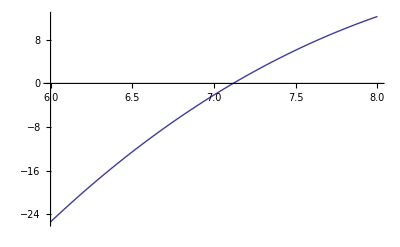

```mathematica
Plot[Mass[FiltedList[[1,1]]+PmT[mF25,Bρ2KEA[B,9,25,mF25]*25,π,0]-FiltedList[[1,3]]-FiltedList[[1,4]]]+mp-mF25-13.26,{B,6,8}]
```

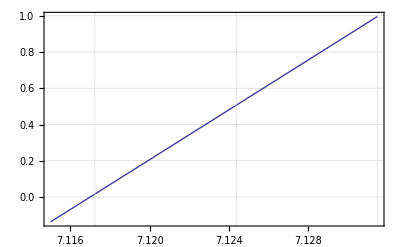

```mathematica
Plot[Bρ2KEA[B,9,25,mF25]-Bρ2KEA[7.117,9,25,mF25],{B,7.115,7.1315},Frame->True,GridLines->{Table[7.1315(1+i),{i,-0.01,0.01,0.001}],Automatic}]
```

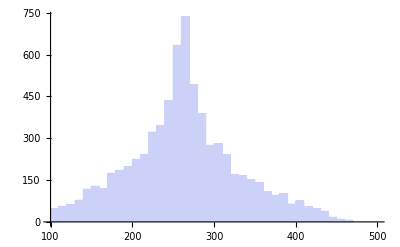

```mathematica
Etot=Table[KE[FiltedList[[i,3]]]+KE[FiltedList[[i,4]]],{i,1,m}];
Histogram[Etot,{100,500,10}]
```

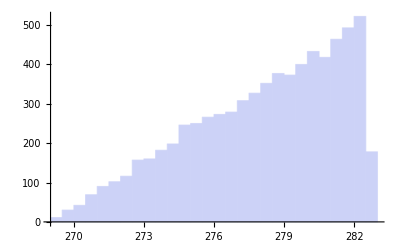

```mathematica
Histogram[Table[KE[FiltedList[[i,2]]]/25,{i,1,m}]]
```

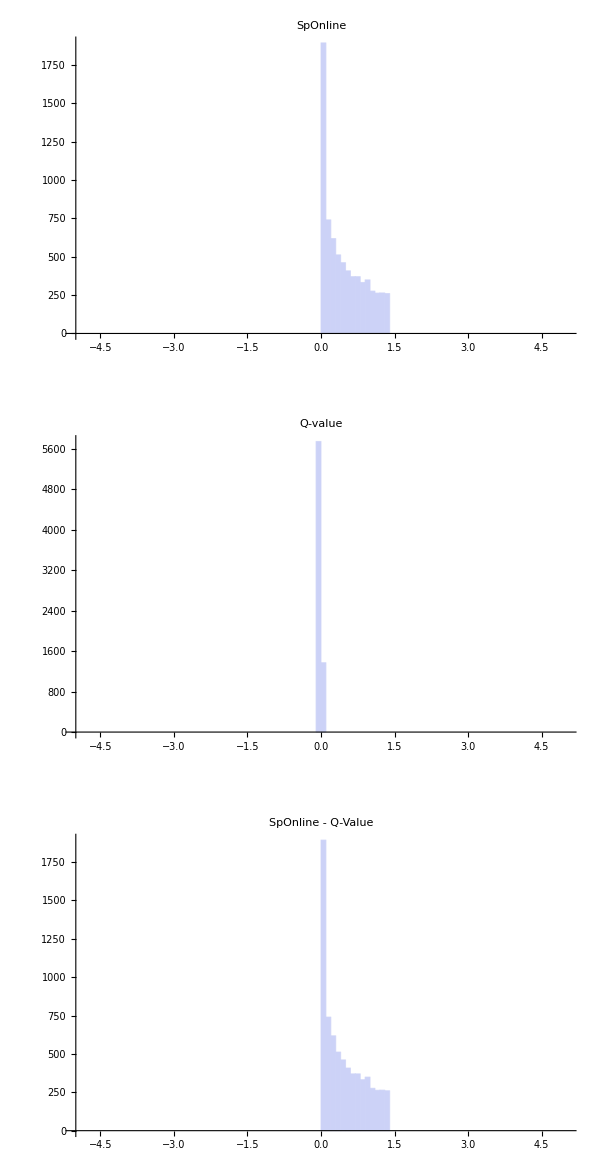

```mathematica
SpF=Table[Sp[FiltedList[[i,1]],FiltedList[[i,2]],FiltedList[[i,3]],FiltedList[[i,4]]],{i,1,m}];
SpOnlineF=Table[SpOnline[FiltedList[[i,3]],FiltedList[[i,4]],β[FiltedList[[i,2]]]],{i,1,m}];
ΔSp=Table[SpOnline[FiltedList[[i,3]],FiltedList[[i,4]],β[FiltedList[[i,2]]]]-Sp[FiltedList[[i,1]],FiltedList[[i,2]],FiltedList[[i,3]],FiltedList[[i,4]]],{i,1,m}];
GraphicsGrid[{
{Histogram[SpOnlineF-13.26,{-5,5,0.1},PlotLabel->"SpOnline"]},
{Histogram[SpF-13.26,{-5,5,0.1}, PlotLabel->"Q-value"]},
{Histogram[ΔSp,{-5,5,0.1}, PlotLabel->"SpOnline - Q-Value"]}},ImageSize->600]
```

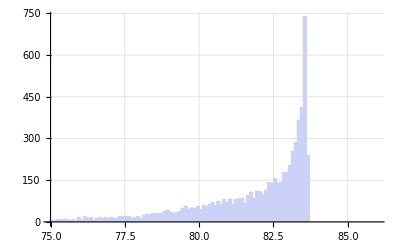

```mathematica
OpAngF=Table[(AngleRev[FiltedList[[i,3]]][[1]]+AngleRev[FiltedList[[i,4]]][[1]])180/π,{i,1,m}];
Histogram[OpAngF,{75,86,0.1},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

```mathematica
Δtof1=RandomVariate[NormalDistribution[0,0.5],m];
Δx1=RandomVariate[NormalDistribution[0,0.2],m];
Δy1=RandomVariate[NormalDistribution[0,0.4],m];
Δtof2=RandomVariate[NormalDistribution[0,0.8],m];
Δx2=RandomVariate[NormalDistribution[0,0.3],m];
Δy2=RandomVariate[NormalDistribution[0,0.4],m];
```

```mathematica
MeasureList=Table[{
FiltedList[[i,1]],
FiltedList[[i,2]],
New4Vector[FiltedList[[i,3]],Δtof1[[i]],Δx1[[i]],Δy1[[i]]],
New4Vector[FiltedList[[i,4]],Δtof2[[i]],Δx2[[i]],Δy2[[i]]]
},{i,1,m}];
```

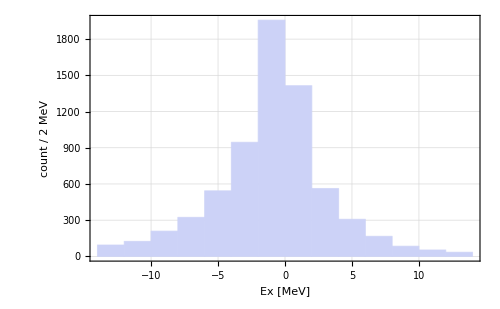

```mathematica
SpM=Table[Sp[MeasureList[[i,1]],MeasureList[[i,2]],MeasureList[[i,3]],MeasureList[[i,4]]],{i,1,m}];
h0=Histogram[SpM-13.26,{-14,14,2},ImageSize->500,Frame->True,GridLines->Automatic,FrameLabel->{"Ex [MeV]","count / 2 MeV"}]
```

```mathematica
Remove[h1,SpM]
```

```mathematica
h1=HistogramList[SpM-13.26,{-14,14,2}];
```

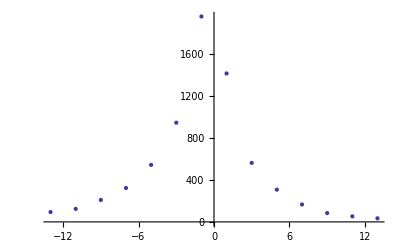

```mathematica
fitdata=Table[{(h1[[1,i]]+h1[[1,i+1]])/2,h1[[2,i]]},{i,1,Length[h1[[2]]]}];
ListPlot[fitdata]
```

```mathematica
FindFit[fitdata,aa Exp[-1/2((xx-bb)/cc)^2],{aa,bb,cc},xx]
```

{aa→1777.23,bb→-0.650686,cc→-2.62691}

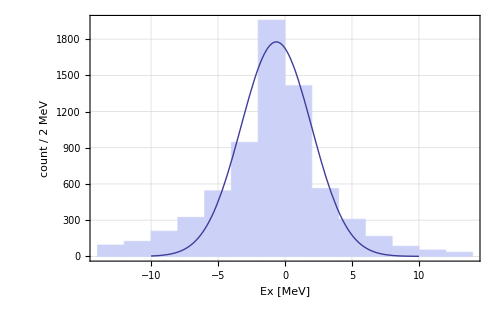

```mathematica
Show[
{h0,
Plot[1777Exp[-1/2((x+0.65)/2.63)^2],{x,-10,10}]
}
]
```

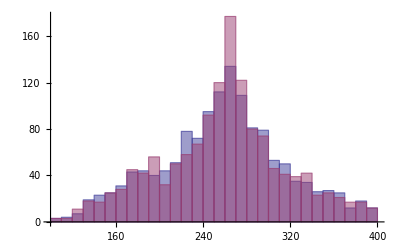

```mathematica
EtotM=Table[KE[MeasureList[[i,3]]]+KE[MeasureList[[i,4]]],{i,1,m}];
Histogram[{EtotM,Etot},{100,400,10}]
```

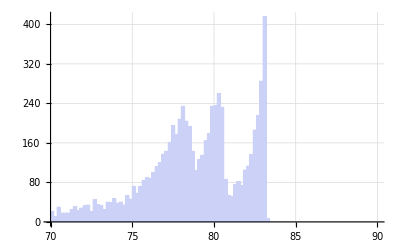

```mathematica
OpAng=Table[(AngleRev[MeasureList[[i,3]]][[1]]+AngleRev[MeasureList[[i,4]]][[1]])180/π,{i,1,m}];
Histogram[OpAng,{70,90,0.2},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

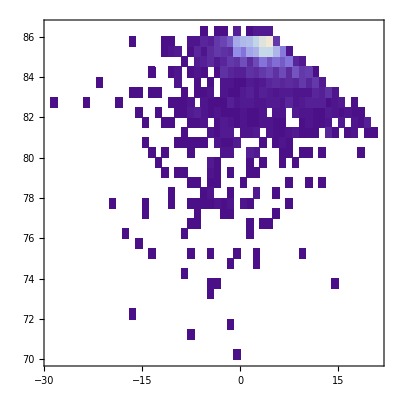

```mathematica
OpAngSp=Table[{SpM[[i]],OpAng[[i]]},{i,1,m}];
DensityHistogram[OpAngSp,{{-30,30,1},{70,100,0.5}}]
```

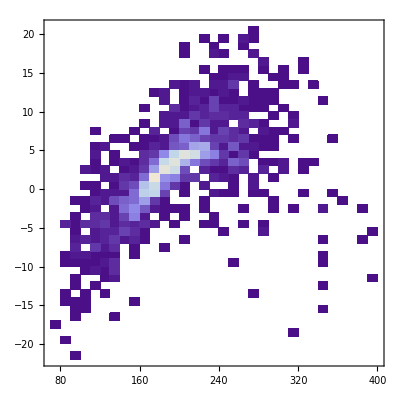

```mathematica
SpEtot=Table[{EtotM[[i]],SpM[[i]]},{i,1,m}];
DensityHistogram[SpEtot,{{0,400,10},{-30,60,1}}]
```